```mathematica
f[x_,y_]:=x^3-y^2+x+y
```

```mathematica
Plot3D[{f[-x,y],f[x,y]},{x,-4,4},{y,-7,7}]
```

-Graphics3D-

```mathematica
Solve[Det[{D[f[x,y],{{x,y}}],D[f[-x,y],{{x,y}}]}]==0]
```

{{x→-ⅈ/(√3)},{x→ⅈ/(√3)},{y→1/2}}

```mathematica
Solve[f[x,y]==c && f[-x,y]==c]
```

{{c→y-y^2,x→0},{c→y-y^2,x→-ⅈ},{c→y-y^2,x→ⅈ}}

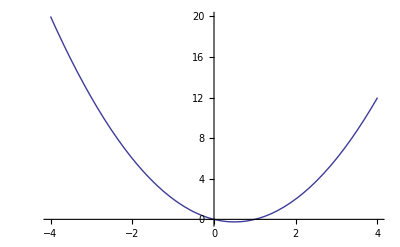

```mathematica
Plot[f[0,y,{y,-4,4}]
```